```mathematica
Chromatics[g_,vertices_]:=Block[
{result={}, 
graph1, graph2, graph3, graph4, graph5, graph6, fullgraph, 
div, div4, first, second, second4,third, fourth, fifth, sixth, full, vert1, vert2, vert3, vert4, vert5, vert6, circle = Rule3Cycle[vertices], newNode, toAdd},


div=ChromaticPolynomial[g,x];
newNode=Max[VertexList[g]]+1;
toAdd=Table[newNode<->vertex,{vertex,vertices}];
fullgraph=Graph[EdgeAdd[g,toAdd]];
full=ChromaticPolynomial[fullgraph,x];

(*double*)
vert1={vertices[[2]]<->vertices[[4]],vertices[[2]]<->vertices[[5]]};
graph1=Graph[EdgeAdd[g,vert1]];
first=ChromaticPolynomial[graph1,x];

(*double 2*)
vert2={vertices[[3]]<->vertices[[5]],vertices[[3]]<->vertices[[1]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=ChromaticPolynomial[graph2,x];
div4=div/.x->4;
second4=second/.x->4;
If [second4 ≠ div4,
(* single *)
vert3={vertices[[4]]<->vertices[[1]]};
graph3=Graph[EdgeAdd[g,vert3]];
third=(ChromaticPolynomial[graph3,x])

,
(* ELSE *)
(* double 2 other direction *)
vert2={vertices[[1]]<->vertices[[3]],vertices[[1]]<->vertices[[4]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=(ChromaticPolynomial[graph2,x]);

(* single other direction *)
vert3={vertices[[3]]<->vertices[[5]]};
graph3=Graph[EdgeAdd[g,vert3]];
third=(ChromaticPolynomial[graph3,x]),
];

(* couples of 1, 2 and 3 solutions *)
vert4 = Join[vert1, vert2];
graph4=Graph[EdgeAdd[g,vert4]];
fourth=(ChromaticPolynomial[graph4,x]);


vert5= Join[vert1, vert3];
graph5=Graph[EdgeAdd[g,vert5]];
fifth=(ChromaticPolynomial[graph5,x]);


vert6= Join[vert2, vert3];
graph6=Graph[EdgeAdd[g,vert6]];
sixth=(ChromaticPolynomial[graph6,x]);

result=Map[Factor[#/((x-1)*(x-2)x)]->(#/24/.x->4)&,{first,second,third, fourth, fifth, sixth,div, full}];
result
]
```

```mathematica
Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
TableForm[Chromatics[empty, deps3[[k,3,2]]], TableHeadings->{{"A","B","C","AB","AC","BC", "Empty", "Result"}, None}]
],{k,2000000,2000010}],k]
```

{A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5)→18
C | (-3+x)^5 (-313+447 x-267 x^2+84 x^3-14 x^4+x^5)→19
AB | (-3+x)^6 (159-166 x+68 x^2-13 x^3+x^4)→7
AC | (-3+x)^5 (-491+664 x-371 x^2+107 x^3-16 x^4+x^5)→5
BC | (-3+x)^5 (-383+542 x-315 x^2+95 x^3-15 x^4+x^5)→9
Empty | (-3+x)^4 (-2+x) (-278+417 x-258 x^2+83 x^3-14 x^4+x^5)→28
Result | (-3+x)^5 (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6)→7,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5)→18
C | (-3+x)^5 (-313+447 x-267 x^2+84 x^3-14 x^4+x^5)→19
AB | (-3+x)^6 (159-166 x+68 x^2-13 x^3+x^4)→7
AC | (-3+x)^5 (-491+664 x-371 x^2+107 x^3-16 x^4+x^5)→5
BC | (-3+x)^5 (-383+542 x-315 x^2+95 x^3-15 x^4+x^5)→9
Empty | (-3+x)^4 (-2+x) (-278+417 x-258 x^2+83 x^3-14 x^4+x^5)→28
Result | (-3+x)^5 (1271-2152 x+1551 x^2-613 x^3+141 x^4-18 x^5+x^6)→7,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^7 (-32+29 x-9 x^2+x^3)→4
C | (-3+x)^7 (-26+24 x-8 x^2+x^3)→6
AB | (-3+x)^6 (187-194 x+77 x^2-14 x^3+x^4)→3
AC | (-3+x)^6 (145-159 x+67 x^2-13 x^3+x^4)→5
BC | (-4+x) (-3+x)^6 (-32+29 x-9 x^2+x^3)→0
Empty | (-3+x)^5 (10-6 x+x^2) (-17+18 x-7 x^2+x^3)→14
Result | (-3+x)^6 (-398+553 x-317 x^2+95 x^3-15 x^4+x^5)→6,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^9 (-2+x)→2
C | (-3+x)^6 (-2+x) (-35+30 x-9 x^2+x^3)→10
AB | (-3+x)^6 (121-142 x+64 x^2-13 x^3+x^4)→1
AC | (-3+x)^6 (145-159 x+67 x^2-13 x^3+x^4)→5
BC | (-4+x) (-3+x)^6 (-2+x) (10-6 x+x^2)→0
Empty | (-3+x)^5 (-2+x) (73-96 x+48 x^2-11 x^3+x^4)→18
Result | (-3+x)^6 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (7-5 x+x^2) (-49+38 x-10 x^2+x^3)→42
C | (-3+x)^5 (-289+430 x-264 x^2+84 x^3-14 x^4+x^5)→23
AB | (-3+x)^6 (151-163 x+68 x^2-13 x^3+x^4)→11
AC | (-3+x)^5 (-483+661 x-371 x^2+107 x^3-16 x^4+x^5)→1
BC | (-3+x)^5 (7-5 x+x^2) (-49+38 x-10 x^2+x^3)→21
Empty | (-3+x)^4 (-2+x) (-262+403 x-255 x^2+83 x^3-14 x^4+x^5)→44
Result | (-3+x)^5 (1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6)→11,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (7-5 x+x^2) (-49+38 x-10 x^2+x^3)→42
C | (-3+x)^5 (-289+430 x-264 x^2+84 x^3-14 x^4+x^5)→23
AB | (-3+x)^6 (151-163 x+68 x^2-13 x^3+x^4)→11
AC | (-3+x)^5 (-483+661 x-371 x^2+107 x^3-16 x^4+x^5)→1
BC | (-3+x)^5 (7-5 x+x^2) (-49+38 x-10 x^2+x^3)→21
Empty | (-3+x)^4 (-2+x) (-262+403 x-255 x^2+83 x^3-14 x^4+x^5)→44
Result | (-3+x)^5 (1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6)→11,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^2 (14561-32343 x+31981 x^2-18457 x^3+6824 x^4-1660 x^5+260 x^6-24 x^7+x^8)→21
C | (-3+x)^4 (1091-1861 x+1354 x^2-543 x^3+128 x^4-17 x^5+x^6)→15
AB | (-3+x)^2 (19633-43279 x+42353 x^2-24034 x^3+8653 x^4-2025 x^5+301 x^6-26 x^7+x^8)→5
AC | (-3+x)^5 (-483+661 x-371 x^2+107 x^3-16 x^4+x^5)→1
BC | (-3+x)^3 (-6534+11879 x-9489 x^2+4332 x^3-1226 x^4+216 x^5-22 x^6+x^7)→6
Empty | (-3+x)^4 (748-1350 x+1045 x^2-448 x^3+113 x^4-16 x^5+x^6)→36
Result | (-3+x)^2 (-46808+118056 x-134183 x^2+90419 x^3-39908 x^4+11995 x^5-2461 x^6+333 x^7-27 x^8+x^9)→24,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-32+29 x-9 x^2+x^3) (-35+30 x-9 x^2+x^3)→20
C | (-3+x)^4 (956-1672 x+1255 x^2-520 x^3+126 x^4-17 x^5+x^6)→12
AB | (-3+x)^4 (13-7 x+x^2) (145-159 x+67 x^2-13 x^3+x^4)→5
AC | (-3+x)^5 (-483+661 x-371 x^2+107 x^3-16 x^4+x^5)→1
BC | (-3+x)^5 (-535+703 x-382 x^2+108 x^3-16 x^4+x^5)→5
Empty | (-3+x)^4 (613-1161 x+946 x^2-425 x^3+111 x^4-16 x^5+x^6)→33
Result | (-3+x)^4 (-4298+8408 x-7188 x^2+3499 x^3-1052 x^4+196 x^5-21 x^6+x^7)→22,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
C | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
AB | (-4+x) (-3+x)^4 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→0
AC | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
BC | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
Empty | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
Result | (-3+x)^6 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
C | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
AB | (-4+x) (-3+x)^4 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→0
AC | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
BC | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
Empty | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
Result | (-3+x)^6 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12,A | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
B | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
C | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
AB | (-4+x) (-3+x)^4 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→0
AC | (-3+x)^5 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12
BC | (-3+x)^4 (-2+x) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→24
Empty | (-3+x)^3 (-2+x)^2 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→48
Result | (-3+x)^6 (-332+498 x-303 x^2+94 x^3-15 x^4+x^5)→12}

```mathematica
Map[CompleteBaseCoeff[#]&,{18 x-39 x^2+29 x^3-9 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5,8 x-20 x^2+18 x^3-7 x^4+x^5,24 x-50 x^2+35 x^3-10 x^4+x^5,18 x-39 x^2+29 x^3-9 x^4+x^5,12 x-28 x^2+23 x^3-8 x^4+x^5,8 x-20 x^2+18 x^3-7 x^4+x^5,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6}]
```

{{0,0,0,0,1,1},{0,0,0,0,2,1},{0,0,0,1,3,1},{0,0,0,0,0,1},{0,0,0,0,1,1},{0,0,0,0,2,1},{0,0,0,1,3,1},{0,0,0,0,1,3,1}}

```mathematica
CompleteBaseCoeff[12 x-28 x^2+23 x^3-8 x^4+x^5]
```

{0,0,0,0,2,1}

```mathematica
Colofours[g_,vertices_]:=Block[
{result={}, 
graph1, graph2, graph3, graph4, graph5, graph6, fullgraph, 
div,  first, second, third, fourth, fifth, sixth, full, vert1, vert2, vert3, vert4, vert5, vert6, circle = Rule3Cycle[vertices], newNode, toAdd},


div=ChromaticPolynomial[g,4]/24;
newNode=Max[VertexList[g]]+1;
toAdd=Table[newNode<->vertex,{vertex,vertices}];
fullgraph=Graph[EdgeAdd[g,toAdd]];
full=ChromaticPolynomial[fullgraph,4]/24;

(*double*)
vert1={vertices[[2]]<->vertices[[4]],vertices[[2]]<->vertices[[5]]};
graph1=Graph[EdgeAdd[g,vert1]];
first=ChromaticPolynomial[graph1,4]/24;

(*double 2*)
vert2={vertices[[3]]<->vertices[[5]],vertices[[3]]<->vertices[[1]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=ChromaticPolynomial[graph2,4]/24;
If [second ≠ div,
(* single *)
vert3={vertices[[4]]<->vertices[[1]]};
graph3=Graph[EdgeAdd[g,vert3]];
third=(ChromaticPolynomial[graph3,4]/24)

,
(* ELSE *)
(* double 2 other direction *)
vert2={vertices[[1]]<->vertices[[3]],vertices[[1]]<->vertices[[4]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=(ChromaticPolynomial[graph2,4]/24);

(* single other direction *)
vert3={vertices[[3]]<->vertices[[5]]};
graph3=Graph[EdgeAdd[g,vert3]];
third=(ChromaticPolynomial[graph3,4]/24),
];

(* couples of 1, 2 and 3 solutions *)
vert4 = Join[vert1, vert2];
graph4=Graph[EdgeAdd[g,vert4]];
fourth=(ChromaticPolynomial[graph4,4]/24);


vert5= Join[vert1, vert3];
graph5=Graph[EdgeAdd[g,vert5]];
fifth=(ChromaticPolynomial[graph5,4]/24);


vert6= Join[vert2, vert3];
graph6=Graph[EdgeAdd[g,vert6]];
sixth=(ChromaticPolynomial[graph6,4]/24);


result={first,second,third, fourth, fifth, sixth,div, full}/div;
result
]
```

```mathematica
$HistoryLength=10
```

10

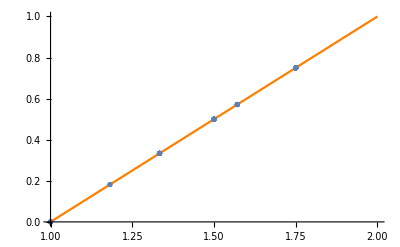

```mathematica
Show[
Plot[x-1,{x,1,2}, PlotStyle->Orange,
PlotRange->All,
GridLines->{{1,7/4},{0,3/4}}],
ListPlot[
Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
With[{t=Colofours[empty, deps3[[k,3,2]]]},
{Total[Take[t,3]],Total[Take[t,{4,6}]]}
]
],{k,1,100}],k],
PlotRange->All,
GridLines->{{1,7/4},{0,3/4}}
]
]
```

```mathematica
DeleteDuplicates[Sort[N[Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
With[{t=Colofours[empty, deps3[[k,3,2]]]},
{Total[Take[t,{1,3}]],Total[Take[t,{4,6}]]}
]
],{k,1,1000}],k]]]]
```

```mathematica
Fit[ {{1.,0.},{1.125,0.125},{1.1818181818181819,0.18181818181818182},{1.2352941176470589,0.23529411764705882},{1.3333333333333333,0.3333333333333333},{1.3823529411764706,0.38235294117647056},{1.4090909090909092,0.4090909090909091},{1.4210526315789473,0.42105263157894735},{1.4375,0.4375},{1.4615384615384615,0.46153846153846156},{1.5,0.5},{1.5714285714285714,0.5714285714285714},{1.6538461538461537,0.6538461538461539},{1.6666666666666667,0.6666666666666666},{1.6956521739130435,0.6956521739130435},{1.75,0.75}},{1,x},x]
```

-1.+1. x

```mathematica
BoolToNum[b_]:=If[b,1,0]
```

```mathematica
ColofoursSlow[g_,vertices_]:=Block[
{result={}, 
graph1, graph2, graph3, graph4, graph5, graph6,  
cond1, cond2, cond3,cond1Excl, cond2Excl, cond3Excl, cond4, cond5, cond6, 
sols,
div,  second,   full, vert1, vert2, vert3, vert4, vert5, vert6, circle = Rule3Cycle[vertices], newNode, toAdd,
record, index
},


div=ChromaticPolynomial[g,4];
newNode=Max[VertexList[g]]+1;
toAdd=Table[newNode<->vertex,{vertex,vertices}];

(*double*)
vert1={vertices[[2]]<->vertices[[4]],vertices[[2]]<->vertices[[5]]};
graph1=Graph[EdgeAdd[g,vert1]];

(*double 2*)
vert2={vertices[[3]]<->vertices[[5]],vertices[[3]]<->vertices[[1]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=(ChromaticPolynomial[graph2,4]/24);
If [second ≠ div,
(* single *)
vert3={vertices[[4]]<->vertices[[1]]};
graph3=Graph[EdgeAdd[g,vert3]];

,
(* ELSE *)
(* double 2 other direction *)
vert2={vertices[[1]]<->vertices[[3]],vertices[[1]]<->vertices[[4]]};
graph2=Graph[EdgeAdd[g,vert2]];

(* single other direction *)
vert3={vertices[[3]]<->vertices[[5]]};
graph3=Graph[EdgeAdd[g,vert3]];
];

(* couples of 1, 2 and 3 solutions *)
vert4 = Join[vert1, vert2];
graph4=Graph[EdgeAdd[g,vert4]];


vert5= Join[vert1, vert3];
graph5=Graph[EdgeAdd[g,vert5]];


vert6= Join[vert2, vert3];
graph6=Graph[EdgeAdd[g,vert6]];

cond1=ToLogical[graph1];
cond2=ToLogical[graph2];
cond3=ToLogical[graph3];
cond4=ToLogical[graph4];
cond5=ToLogical[graph5];
cond6=ToLogical[graph6];
cond1Excl=cond1 && ! cond4 && ! cond5;
cond2Excl=cond2 && ! cond4 && ! cond6;
cond3Excl=cond3 && ! cond5 && ! cond6;

sols=GraphSolutions2[g,vertices];
result=Table[
{ 
BoolToNum[cond1Excl/.s], 
BoolToNum[cond2Excl/.s], 
BoolToNum[cond3Excl/.s], 
BoolToNum[cond4/.s], 
BoolToNum[cond5/.s], 
BoolToNum[cond6/.s],
BoolToNum[cond1/.s], 
BoolToNum[cond2/.s], 
BoolToNum[cond3/.s]
},{s,sols}];
record=result[[1]];
For[i=2,i≤Length[result],i++,
record=record+result[[i]]
];
record/div
]
```

```mathematica
Length[deps3]
```

2436995

```mathematica
hale=Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
With[{t=ColofoursSlow[empty, deps3[[k,3,2]]]},
t
]
],{k,1,1000}],k]
```

{{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{3/11,1/11,5/11,0,2/11,0,5/11,1/11,7/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/14,0,5/14,0,3/14,5/14,2/7,5/14,13/14},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/9,2/9,1/3,1/9,1/9,1/9,1/3,4/9,5/9},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/11,1/11,7/11,0,2/11,0,3/11,1/11,9/11},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{0,1/8,1/8,1/8,1/4,3/8,3/8,5/8,3/4},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/18,5/18,1/18,5/18,0,2/3,1/9,5/9},{2/7,1/14,1/14,3/14,5/14,0,6/7,2/7,3/7},{0,0,2/3,0,1/18,5/18,1/18,5/18,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/14,0,5/14,0,3/14,5/14,2/7,5/14,13/14},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{3/17,5/17,5/17,2/17,0,2/17,5/17,9/17,7/17},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{3/11,1/11,5/11,0,2/11,0,5/11,1/11,7/11},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{0,0,1/4,0,5/12,1/3,5/12,1/3,1},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/9,5/9,0,1/9,2/9,1/9,1/3,8/9},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,2/11,9/22,0,2/11,5/22,2/11,9/22,9/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{2/9,1/9,1/3,1/9,1/9,1/9,4/9,1/3,5/9},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{3/16,1/8,9/16,0,1/16,1/16,1/4,3/16,11/16},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{2/9,2/9,2/9,1/9,1/9,1/9,4/9,4/9,4/9},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{0,0,2/3,0,5/18,1/18,5/18,1/18,1},{0,1/14,5/14,0,5/14,3/14,5/14,2/7,13/14},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/9,5/9,0,1/9,2/9,1/9,1/3,8/9},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/14,2/7,1/14,3/14,0,5/14,2/7,6/7,3/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/9,2/9,1/3,1/9,1/9,1/9,1/3,4/9,5/9},{1/9,0,5/9,0,2/9,1/9,1/3,1/9,8/9},{0,0,1/4,1/8,1/4,3/8,3/8,1/2,7/8},{0,0,3/7,0,3/14,5/14,3/14,5/14,1},{1/17,3/17,9/17,0,2/17,2/17,3/17,5/17,13/17},{0,0,9/16,0,3/16,1/4,3/16,1/4,1},{1/12,1/4,1/3,1/12,1/12,1/6,1/4,1/2,7/12},{1/8,3/16,9/16,0,1/16,1/16,3/16,1/4,11/16},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{0,1/8,1/8,1/8,1/4,3/8,3/8,5/8,3/4},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/11,1/11,7/11,0,2/11,0,3/11,1/11,9/11},{2/7,1/14,1/14,3/14,5/14,0,6/7,2/7,3/7},{1/3,1/18,5/18,1/18,5/18,0,2/3,1/9,5/9},{1/3,5/18,1/18,5/18,1/18,0,2/3,5/9,1/9},{1/3,5/18,1/18,5/18,1/18,0,2/3,5/9,1/9},{1/3,1/18,5/18,1/18,5/18,0,2/3,1/9,5/9},{2/7,1/14,1/14,3/14,5/14,0,6/7,2/7,3/7},{0,0,9/26,0,6/13,5/26,6/13,5/26,1},{1/23,0,6/23,0,11/23,5/23,12/23,5/23,22/23},{0,0,21/34,1/34,11/34,1/34,6/17,1/17,33/34},{1/3,1/18,5/18,1/18,5/18,0,2/3,1/9,5/9},{1/5,0,2/15,2/15,7/15,1/15,4/5,1/5,2/3},{5/19,0,6/19,0,7/19,1/19,12/19,1/19,14/19},{2/7,1/14,1/14,3/14,5/14,0,6/7,2/7,3/7},{1/3,5/18,1/18,5/18,1/18,0,2/3,5/9,1/9},{1/3,5/18,1/18,5/18,1/18,0,2/3,5/9,1/9},{2/7,1/14,1/14,3/14,5/14,0,6/7,2/7,3/7},{0,0,3/7,1/14,1/7,5/14,3/14,3/7,13/14},{0,0,1/4,1/8,1/4,3/8,3/8,1/2,7/8},{1/11,1/11,7/11,0,2/11,0,3/11,1/11,9/11},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{1/9,2/9,1/3,1/9,1/9,1/9,1/3,4/9,5/9},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/9,2/9,1/3,1/9,1/9,1/9,1/3,4/9,5/9},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{0,0,1/4,1/8,1/4,3/8,3/8,1/2,7/8},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{1/11,1/11,7/11,0,2/11,0,3/11,1/11,9/11},{1/17,3/17,9/17,0,2/17,2/17,3/17,5/17,13/17},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{1/11,1/11,7/11,0,2/11,0,3/11,1/11,9/11},{0,1/5,2/15,2/15,1/15,7/15,1/5,4/5,2/3},{1/8,3/16,9/16,0,1/16,1/16,3/16,1/4,11/16},{1/9,0,5/9,0,2/9,1/9,1/3,1/9,8/9},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/9,2/9,1/3,1/9,1/9,1/9,1/3,4/9,5/9},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{0,0,1/4,1/8,1/4,3/8,3/8,1/2,7/8},{0,1/12,1/6,1/12,1/6,1/2,1/4,2/3,5/6},{0,1/6,1/12,1/6,1/12,1/2,1/4,5/6,2/3},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,1/23,6/23,0,5/23,11/23,5/23,12/23,22/23},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/8,0,1/8,1/8,3/8,1/4,5/8,3/8,3/4},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{3/17,1/17,9/17,0,2/17,2/17,5/17,3/17,13/17},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{3/13,2/13,2/13,3/13,3/13,0,9/13,5/13,5/13},{1/4,1/8,3/16,1/8,3/16,1/8,9/16,3/8,1/2},{5/17,3/17,5/17,2/17,2/17,0,9/17,5/17,7/17},{1/4,3/16,1/8,3/16,1/8,1/8,9/16,1/2,3/8},{1/15,0,4/15,1/5,1/3,2/15,3/5,1/3,11/15},{3/14,3/14,0,2/7,1/7,1/7,9/14,9/14,2/7},{1/13,0,7/26,0,7/26,5/13,9/26,5/13,12/13},{1/19,0,10/19,1/19,7/19,0,9/19,1/19,17/19},{1/13,0,7/26,0,7/26,5/13,9/26,5/13,12/13},{1/13,1/13,5/13,2/13,3/13,1/13,6/13,4/13,9/13},{1/7,1/14,3/14,1/14,3/14,2/7,3/7,3/7,5/7},{1/4,3/16,7/16,1/16,1/16,0,3/8,1/4,1/2},{1/7,3/14,1/14,3/14,1/14,2/7,3/7,5/7,3/7},{1/7,3/14,1/14,3/14,1/14,2/7,3/7,5/7,3/7},{1/4,1/4,1/6,1/6,1/12,1/12,1/2,1/2,1/3},{1/7,1/14,3/14,1/14,3/14,2/7,3/7,3/7,5/7},{0,0,3/7,1/14,5/14,1/7,3/7,3/14,13/14},{0,0,13/22,1/22,5/22,3/22,3/11,2/11,21/22},{1/4,3/16,7/16,1/16,1/16,0,3/8,1/4,1/2},{1/15,1/5,1/15,4/15,1/15,1/3,2/5,4/5,7/15},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{0,1/14,5/14,0,5/14,3/14,5/14,2/7,13/14},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{0,1/18,11/18,0,5/18,1/18,5/18,1/9,17/18},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{0,0,3/7,1/7,3/14,3/14,5/14,5/14,6/7},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{0,1/15,4/15,0,1/3,1/3,1/3,2/5,14/15},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{1/8,1/8,0,1/4,1/4,1/4,5/8,5/8,1/2},{3/11,3/11,3/11,2/11,0,0,5/11,5/11,3/11},{1/5,3/10,0,3/10,0,1/5,1/2,4/5,1/5},{1/7,0,2/7,1/7,3/7,0,5/7,1/7,5/7},{1/5,0,3/10,0,3/10,1/5,1/2,1/5,4/5},{0,1/12,1/6,1/4,1/6,1/3,5/12,2/3,2/3},{1/8,0,1/8,1/8,3/8,1/4,5/8,3/8,3/4},{0,1/10,2/5,1/10,1/10,3/10,1/5,1/2,4/5},{0,1/8,1/8,1/8,1/8,1/2,1/4,3/4,3/4},{0,1/8,1/8,1/8,1/8,1/2,1/4,3/4,3/4},{0,1/12,7/12,0,1/6,1/6,1/6,1/4,11/12},{1/9,1/9,4/9,0,1/9,2/9,2/9,1/3,7/9},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/9,5/9,0,1/9,2/9,1/9,1/3,8/9},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{2/9,2/9,2/9,1/9,1/9,1/9,4/9,4/9,4/9},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/14,0,5/14,0,3/14,5/14,2/7,5/14,13/14},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,5/19,6/19,0,1/19,7/19,1/19,12/19,14/19},{0,5/18,7/18,0,1/18,5/18,1/18,5/9,13/18},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,5/18,7/18,0,1/18,5/18,1/18,5/9,13/18},{0,5/18,7/18,0,1/18,5/18,1/18,5/9,13/18},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/13,2/13,4/13,0,3/13,3/13,4/13,5/13,10/13},{0,0,9/16,0,1/4,3/16,1/4,3/16,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/14,2/7,1/14,3/14,0,5/14,2/7,6/7,3/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{3/16,1/8,9/16,0,1/16,1/16,1/4,3/16,11/16},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,0,1/3,5/12,1/3,5/12,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,0,1/3,5/12,1/3,5/12,1},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/14,2/7,1/14,3/14,0,5/14,2/7,6/7,3/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,5/18,7/18,0,1/18,5/18,1/18,5/9,13/18},{0,5/18,7/18,0,1/18,5/18,1/18,5/9,13/18},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/18,5/18,1/18,5/18,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/18,5/18,1/18,5/18,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{7/22,1/11,2/11,3/22,3/11,0,8/11,5/22,5/11},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/14,0,5/14,0,3/14,5/14,2/7,5/14,13/14},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{2/9,1/9,1/3,1/9,1/9,1/9,4/9,1/3,5/9},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/14,0,5/14,0,3/14,5/14,2/7,5/14,13/14},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{0,0,1/4,0,1/3,5/12,1/3,5/12,1},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{0,1/6,1/12,1/4,1/12,5/12,1/3,5/6,7/12},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{0,0,1/4,1/8,3/8,1/4,1/2,3/8,7/8},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/4,0,1/3,5/12,1/3,5/12,1},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{0,0,1/2,1/10,3/10,1/10,2/5,1/5,9/10},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{0,0,1/2,0,2/5,1/10,2/5,1/10,1},{1/7,0,2/7,0,3/7,1/7,4/7,1/7,6/7},{1/3,1/6,1/6,1/6,1/6,0,2/3,1/3,1/3},{1/7,1/7,1/7,2/7,1/7,1/7,4/7,4/7,3/7},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{5/17,0,11/34,0,11/34,1/17,21/34,1/17,12/17},{5/23,0,2/23,5/23,11/23,0,21/23,5/23,13/23},{0,0,21/34,0,1/34,6/17,1/34,6/17,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{1/11,3/11,5/11,0,0,2/11,1/11,5/11,7/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,2/3,0,1/6,1/6,1/6,1/6,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/7,2/7,0,1/7,3/7,1/7,4/7,6/7},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/7,2/7,1/7,0,3/7,1/7,5/7,5/7},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{0,1/4,0,1/4,0,1/2,1/4,1,1/2},{1/5,1/5,3/5,0,0,0,1/5,1/5,3/5},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/2,0,1/10,2/5,1/10,2/5,1},{1/11,1/11,7/11,0,0,2/11,1/11,3/11,9/11},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,3/10,1/5,1/10,0,2/5,1/10,4/5,3/5},{0,3/13,4/13,1/13,0,5/13,1/13,9/13,9/13},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,0,1/4,0,1/4,1/2,1/4,1/2,1},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,1/6,1/2,0,1/6,1/6,1/6,1/3,5/6},{0,0,1/4,0,1/4,1/2,1/4,1/2,1}}

```mathematica
N[Mean[hale]]
```

{0.0755984,0.116293,0.297557,0.0843636,0.158498,0.26769,0.31846,0.468347,0.723745}

```mathematica
Total[{0.0755983669061977,0.11629335278864657,0.2975565978488764}]
```

0.489448

```mathematica
Sort[Tally[Table[{Total[Take[r,3]],Total[Take[r,{4,6}]]},{r, hale}]]]
```

{{{1/4,3/4},379},{{7/23,16/23},3},{{1/3,2/3},5},{{9/26,17/26},3},{{3/7,4/7},122},{{1/2,1/2},103},{{7/13,6/13},4},{{9/16,7/16},4},{{11/19,8/19},3},{{13/22,9/22},3},{{21/34,13/34},3},{{2/3,1/3},252},{{13/17,4/17},5},{{9/11,2/11},25},{{7/8,1/8},6},{{1,0},80}}

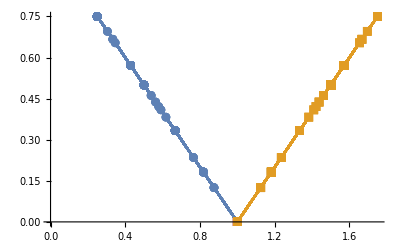

```mathematica
ListLinePlot[{Table[{Total[Take[r,3]],Total[Take[r,{4,6}]]},{r, hale}],Table[{Total[Take[r,{7,9}]],Total[Take[r,{4,6}] ]},{r, hale}]}, PlotMarkers->Automatic]
```

```mathematica
DeleteDuplicates[Sort[Table[Total[r],{r, hale}]]]
```

{1}

```mathematica
Table[{Min[Take[hale,{k}]]->Max[Take[hale,{k}]]},{k,1,9}]
```

{{0→1},{0→1},{0→1},{0→3/5},{0→1},{0→2/3},{0→1},{0→6/7},{0→5/6}}

```mathematica
{Min[Map[Total[Take[#,{1,3}]]&,hale]]->Max[Map[Total[Take[#,{1,3}]]&,hale]]}
```

{1/4→1}

```mathematica
{Min[Map[Total[Take[#,{4,6}]]&,hale]]->Max[Map[Total[Take[#,{4,6}]]&,hale]]}
```

{0→3/4}

```mathematica
DeleteDuplicates[Sort[Table[{Total[Take[r,5]],Total[Take[r,{6,6}]]},{r, hale}]]]
```

{{1/2,1/2},{12/23,11/23},{8/15,7/15},{4/7,3/7},{7/12,5/12},{3/5,2/5},{8/13,5/13},{5/8,3/8},{12/19,7/19},{9/14,5/14},{11/17,6/17},{2/3,1/3},{7/10,3/10},{5/7,2/7},{13/18,5/18},{3/4,1/4},{10/13,3/13},{17/22,5/22},{7/9,2/9},{18/23,5/23},{11/14,3/14},{4/5,1/5},{21/26,5/26},{13/16,3/16},{9/11,2/11},{5/6,1/6},{6/7,1/7},{19/22,3/22},{13/15,2/15},{7/8,1/8},{15/17,2/17},{8/9,1/9},{9/10,1/10},{11/12,1/12},{12/13,1/13},{14/15,1/15},{15/16,1/16},{16/17,1/17},{17/18,1/18},{18/19,1/19},{33/34,1/34},{1,0}}

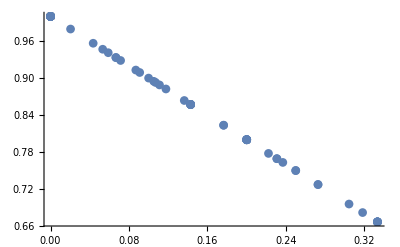

```mathematica
ListPlot[Table[{Total[Take[r,1]],Total[Take[r,{2,6}]]},{r, hale}], PlotMarkers->Automatic]
```

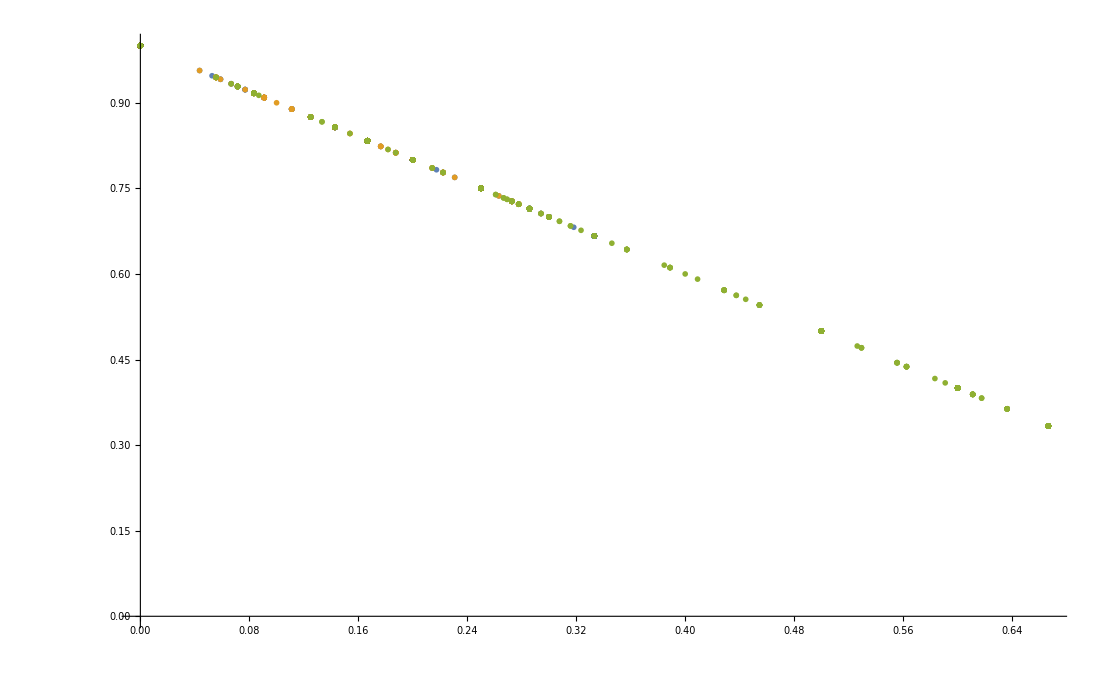

```mathematica
ListPlot[Table[
Table[Tooltip[{Total[Take[r,{k,k}]],Total[Drop[Drop[r,{7,9}],{k}]]},k],{r, hale}]
,{k,1,3}],  PlotRange->All]
```

```mathematica
BoolToChar[b_]:=If[b,"+","-"]
```

```mathematica
ColofoursSlowWithPictures[g_,vertices_]:=Block[
{result={}, 
graph1, graph2, graph3, graph4, graph5, graph6,  
cond1, cond2, cond3,cond1Excl, cond2Excl, cond3Excl, cond4, cond5, cond6, 
sols,
div,  second,   full, vert1, vert2, vert3, vert4, vert5, vert6, circle = Rule3Cycle[vertices], newNode, toAdd,
record, index
},


div=ChromaticPolynomial[g,4];
newNode=Max[VertexList[g]]+1;
toAdd=Table[newNode<->vertex,{vertex,vertices}];

(*double*)
vert1={vertices[[2]]<->vertices[[4]],vertices[[2]]<->vertices[[5]]};
graph1=Graph[EdgeAdd[g,vert1]];

(*double 2*)
vert2={vertices[[3]]<->vertices[[5]],vertices[[3]]<->vertices[[1]]};
graph2=Graph[EdgeAdd[g,vert2]];
second=(ChromaticPolynomial[graph2,4]/24);
If [second ≠ div,
(* single *)
vert3={vertices[[4]]<->vertices[[1]]};
graph3=Graph[EdgeAdd[g,vert3]];

,
(* ELSE *)
(* double 2 other direction *)
vert2={vertices[[1]]<->vertices[[3]],vertices[[1]]<->vertices[[4]]};
graph2=Graph[EdgeAdd[g,vert2]];

(* single other direction *)
vert3={vertices[[3]]<->vertices[[5]]};
graph3=Graph[EdgeAdd[g,vert3]];
];

(* couples of 1, 2 and 3 solutions *)
vert4 = Join[vert1, vert2];
graph4=Graph[EdgeAdd[g,vert4]];


vert5= Join[vert1, vert3];
graph5=Graph[EdgeAdd[g,vert5]];


vert6= Join[vert2, vert3];
graph6=Graph[EdgeAdd[g,vert6]];

cond1=ToLogical[graph1];
cond2=ToLogical[graph2];
cond3=ToLogical[graph3];
cond4=ToLogical[graph4];
cond5=ToLogical[graph5];
cond6=ToLogical[graph6];
cond1Excl=cond1 && ! cond4 && ! cond5;
cond2Excl=cond2 && ! cond4 && ! cond6;
cond3Excl=cond3 && ! cond5 && ! cond6;

sols=GraphSolutions2[g,vertices];
result=Table[
Join[
With[
{colors=Map[IndexToColor[#[[2]]]&,s]},
{colors[[vertices[[1]] ]],colors[[vertices[[2]] ]],colors[[vertices[[3]] ]],colors[[vertices[[4]] ]],colors[[vertices[[5]] ]]}
],
{ 
BoolToChar[cond1Excl/.s], 
BoolToChar[cond2Excl/.s], 
BoolToChar[cond3Excl/.s], 
BoolToChar[cond4/.s], 
BoolToChar[cond5/.s], 
BoolToChar[cond6/.s](*,
BoolToChar[cond1/.s], 
BoolToChar[cond2/.s], 
BoolToChar[cond3/.s]*)
}
],{s,sols}];
result
]
```

```mathematica
Monitor[

Table[
With[
{empty=EdgeDelete[ReadGrof[deps3[[k,1]]],deps3[[k,3,3]]],cycle=deps3[[k,3,2]]},
With[{t=ColofoursSlowWithPictures[empty, deps3[[k,3,2]]]},
TableForm[
Select[t,#[[7]]=="+"||#[[6]]=="+"||#[[8]]=="+"&], TableSpacing->{0, 0}]

]
],{k,100,100}],k]
```

{RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | - | + | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | - | + | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | + | - | - | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | - | - | + | - | - | -
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | + | - | - | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | - | - | + | - | - | -
RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | - | + | - | - | - | -}